```mathematica
(*2. Считать данные из полученного входного файла в системе Wolfram Mathematica (учесть, что размерность графа может быть любой и параметры bi могут идти в произвольном порядке).*)
```

```mathematica
inFileName=StringJoin[NotebookDirectory[],"input.txt"];
fileStream=OpenRead[inFileName];
Is=Read[fileStream,{Word,Number}][[2]];
Us=Read[fileStream,{Word,Number}][[2]];
U=ReadList[fileStream,Expression,Us];
weight=ReadList[fileStream,String,Is];
weight=Sort[Table[StringSplit[weight[[i]],{"b","_","/*","*/ ", " "}], {i,Is}]];
UDirect=Table[U[[i,1]]->U[[i,2]],{i,Us}]
Close[fileStream];
```

{1->2,3->1,1->4,5->2,1->6,3->6,3->7,4->3,5->3,5->6,6->2,7->1,7->4}

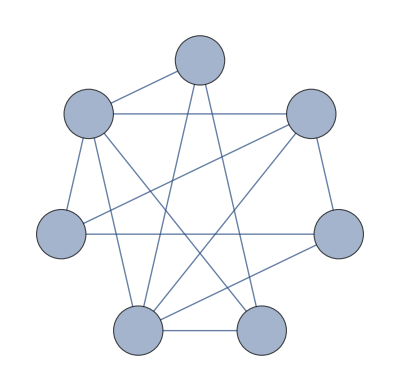

```mathematica
(*3. По полученным данным создать ориентированный граф с заданием стилей/*)
g = Graph[UDirect, GraphLayout->"CircularEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick]
```

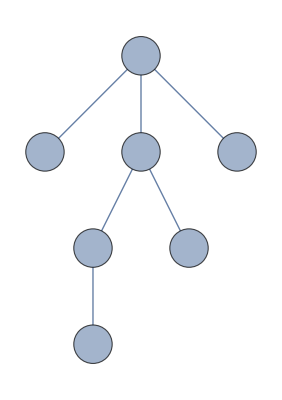

{4,1,3,5}

```mathematica
e ={5->2,5->3,5->6,3->1,3->7,1->4};
g= Graph[e, GraphLayout->{"LayeredEmbedding","RootVertex"->5},VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick]
p={3,5,5,1,0,5,3};
depth={2,1,1,3,0,1,2};

NestList[p[[#]]&,4,depth[[4]]];
NestWhileList[p[[#]]&,4,depth[[#]]>0&];
h[x_]:=Module[{u},
u=NestWhileList[p[[#]]&,x,depth[[#]]>0&];
Return[u]];
h[4]
```

## Лабораторная 4.

```mathematica
(*1. Построить покрывающее дерево для индивидуального графа (от произвольно заданного узла).*)
ug=UndirectedGraph[g];
Graph[ug,GraphLayout->"CircularEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeStyle->Thick];
DepthFirstScan[ug,1];
Ut=TreeGraph[VertexList[ug],%];
EdgeList[Ut]
(*HighlightGraph[ug,TreeGraph[VertexList[ug],%],GraphLayout->"CircularEmbedding",EdgeStyle->Thick, VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28]];*)(*//HighlightGraph[%,#]&*)
```

{5<->2,1<->3,3<->4,3<->5,2<->6,4<->7}

```mathematica
(*3. Построить списковые структуры хранения корневого дерева (список узлов, список предков, список направлений, список глубин узлов, список связи или династического обхода;корень дерева-узел, от которого строили покрывающее дерево, либо любой произвольный узел.*)
pred=ConstantArray[0,Is];(*список предков*)
dir=ConstantArray[0,Is];(*список направлений*)
depth=ConstantArray[0,Is]; (*список глубин узлов*)
dinast=ConstantArray[0,Is];(*династичесий обход*)
posl={};                                            (*последовательность обхода*)
RootTree={};                                   (*корневое дерево*)
Ut={};                                               (*покрывающее дерево*)
root=1;
DepthFirstScan[ug,root,{"FrontierEdge"->Function[edge,{
pred[[edge[[2]]]]=edge[[1]],
depth[[edge[[2]]]]=depth[[edge[[1]]]] + 1,
{i=edge[[1]]->edge[[2]],AppendTo[RootTree,i],If[MemberQ[UDirect,i],{AppendTo[Ut,i],dir[[edge[[2]]]]=1},{AppendTo[Ut,edge[[2]]->edge[[1]]],dir[[edge[[2]]]]=-1}]}
}],
"PrevisitVertex"->Function[vertex,{If[posl≠{},dinast[[posl[[-1]]]]=vertex],AppendTo[posl,vertex]}]
}];
dinast[[posl[[-1]]]]=root;
(*Print[Range[Is]];
Print[pred];
Print[depth];
Print[dir];
Print[dinast];
Print[posl];*)
```

```mathematica
(*2. Вывести полученное множество дуг покрывающего дерева Ut и множество дуг U\Ut.*)
Print[UDirect]
Print[Ut]
Print[Complement[UDirect,Ut]]
```

{1->2,3->1,1->4,5->2,1->6,3->6,3->7,4->3,5->3,5->6,6->2,7->1,7->4}

{3->1,4->3,7->4,5->3,5->2,6->2}

{1->2,1->4,1->6,3->6,3->7,5->6,7->1}

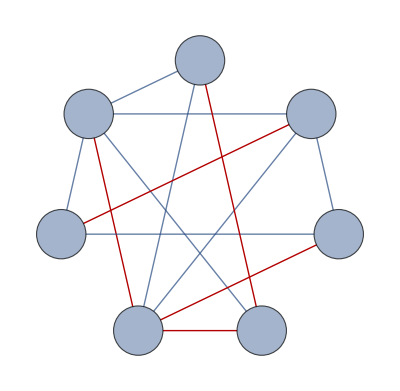

```mathematica
(*4. Вывести картинки:
-исходный граф с подсвеченными дугами покрывающего дерева.*)

Graph[g,GraphHighlight->EdgeList[Ut],GraphLayout->"CircularEmbedding",EdgeStyle->Thick, VertexLabels->Placed["Name",Center], VertexSize->0.4,VertexLabelStyle-> Directive[Italic, 28]]
```

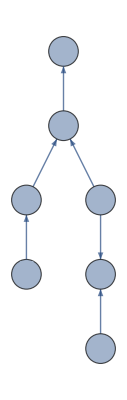

```mathematica
(*4. Вывести картинки:
-покрывающее дерево с использованием layout для деревьев.*)
Graph[Ut,GraphLayout->{"LayeredEmbedding","RootVertex"->root}, EdgeStyle->Thick, VertexLabels->Placed["Name",Center], VertexSize->0.4,VertexLabelStyle-> Directive[Italic, 28]]
```

```mathematica
(*4. Вывести картинки:
-корневое дерево с подсвеченным корнем.*)
```

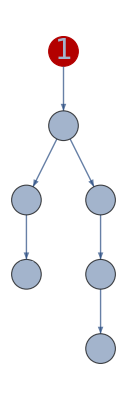

```mathematica
TreeGraph[RootTree,GraphHighlight->root,GraphLayout->{"LayeredEmbedding","RootVertex"->root},EdgeStyle->Thick, VertexLabels->Placed["Name",Center], VertexSize->0.4,VertexLabelStyle-> Directive[Italic, 28]]
```

```mathematica
(*5. Списковые структуры вывести в виде таблицы (список связи или династического обхода можно не встраивать в таблицу,а вывести отдельным списком).*)
Grid[{Prepend[Range[Is],"i"],Prepend[pred,"pred[i]"],Prepend[depth,"depth[i]"],Prepend[dir,"dir[i]"],Prepend[dinast,"dinast[i]"]},Frame->All,ItemStyle->{{Bold},{Bold}}]
Print[posl]
```

i | 1 | 2 | 3 | 4 | 5 | 6 | 7
pred[i] | 0 | 5 | 1 | 3 | 3 | 2 | 4
depth[i] | 0 | 3 | 1 | 2 | 2 | 4 | 3
dir[i] | 0 | 1 | -1 | -1 | -1 | -1 | -1
dinast[i] | 3 | 6 | 4 | 7 | 2 | 1 | 5

{1,3,4,7,5,2,6}